## Time impulse multiple scattering from 2D disks

```mathematica
ClearAll["Global`*"]
Get[NotebookDirectory[]<>"../src/MultipleScattering2D.wl"];
```

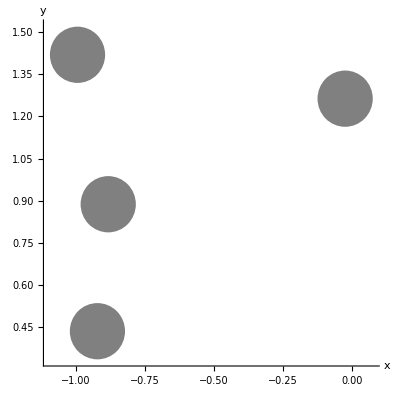

```mathematica
radius=0.1;
N0=3;
NParticles=4;
width=3;
height=2;

Xs =GenerateParticles[NParticles,radius,{{-width/2,width/2},{0,height}}];
DrawScatterers[Xs,0.1]
```

```mathematica
(*Warning takes a while!*)
options={
"MaxFrequencySamples"-> 45,
"PrintChecks"-> False,
"SaveGIF"-> True,
"SaveData"-> True,
"MaxFrequency"-> 1./radius,
"MaxTime"-> 2,
(*"MaxTime"-> 10,*)
(*"MeshSize"->radius/3,*)
"MeshSize"->radius,
"BoundaryCondition"-> "Dirichlet",(*"BoundaryCondition"-> "Neumann",*)
(*"MaxTimeSamples"-> 20*)
"MaxTimeSamples"-> 3
(*,"MaxRadius"->3*)
};
{{{x0,x1},{y0,y1}},listWaves}= ListWavesDueToImpulse[Xs, radius,N0,options];
```

```mathematica
options
```

{PrintChecks→False,SaveGIF→True,SaveData→True,MaxFrequency→10.,MaxTime→2,MeshSize→0.1,BoundaryCondition→Dirichlet,MaxTimeSamples→3}

### Import wave and then plot

```mathematica
(*Import waves combined in a rectangle*)
{Header,options,listWaves}=ImportListWaves[Length[Xs],N0,"MaxFrequencySamples"/.options];
options (* <- extra info added to options, have a look*)
```

{PrintChecks→False,SaveGIF→True,SaveData→True,MaxFrequency→10.,MaxTime→2.,MeshSize→0.1,BoundaryCondition→Dirichlet,MaxTimeSamples→3.,ImpulsePosition→{0.,0.},PlotAmplitudeRatio→0.8,MaxFrequencySamples→45.,MaxRadius→2.97255,ImpulseFunction→(If[0.≤#1≤0.310707,1.,0.]&),ImpulsePeriod→0.310707,AspectRatio→0.863215,RangeTime→{0.,0.312778,0.625557,0.938335,1.25111,1.56389}}

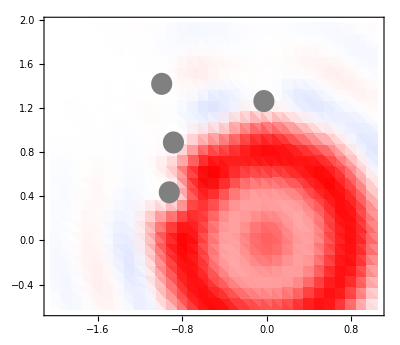

```mathematica
plotSequence= ListPlotSequence[listWaves, If["RangeTime"/.options, "RangeTime"/.options, {}],options];
listplots= (Show@@#)&/@Thread[{plotSequence,DrawScatterers[Xs,0.1]}];
listplots[[4]]
```

```mathematica
(*Import scattered wave from each scatterer independantly*)
(*currently has some minor bug*)
(*{Header,listCylindricalWaves }=ImportListCylindricalWave[Length[Xs],N0,"MaxFrequencySamples"/.options];
{{{x0,x1},{y0,y1}},data}= CombineWaves[{"SourcePosition"/.options}~Join~Xs,listCylindricalWaves, "PlotAmplitude"-> .8,"MeshSize"-> .1/2];*)
```

Import::nffil: File not found during Import.

Set::shape: Lists {{{x0,x1},{y0,y1}},data} and CombineWaves[{SourcePosition,{-0.922471,0.436211},{-0.0253203,1.26296},{-0.88336,0.887645},{-0.994602,1.41898}},$Failed,PlotAmplitude→0.8,MeshSize→0.05] are not the same shape.